```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/poincare/Dropbox/Documentos/DMKM/02 Lyon/CMS/PR

```mathematica
exp=Flatten[Import["exp2.xlsx"]];Length[exp]
```

1089

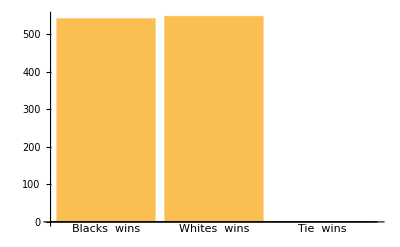

```mathematica
BarChart[Tally[exp][[All,2]],ChartLabels->Tally[exp][[All,1]]](*1089 Tries in a 9x9 size *)
```

```mathematica
exp4=Flatten[Import["exp3.xlsx"]];Length[exp4]
```

570

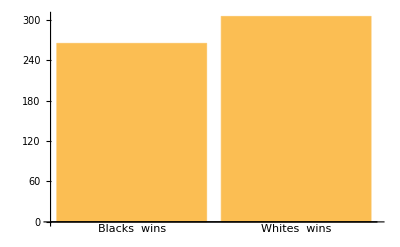

```mathematica
BarChart[Tally[exp4][[All,2]],ChartLabels->Tally[exp4][[All,1]]] (*19x19*)
```

```mathematica
hist1=Import["hist3.csv"];
```

```mathematica
hist1[[All,2]];
N[Mean[hist1[[All,2]]]]
N[Mean[hist1[[All,3]]]]
```

2886.52

2941.15

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
StudentTCI[Mean[hist1[[All,2]]],StandardDeviation[hist1[[All,2]]],Length[hist1[[All,2]]]-1]
```

{1066.82,4617.21}

```mathematica
LocationTest[{hist1[[All,2]],hist1[[All,3]]},0]
```

0.0235406

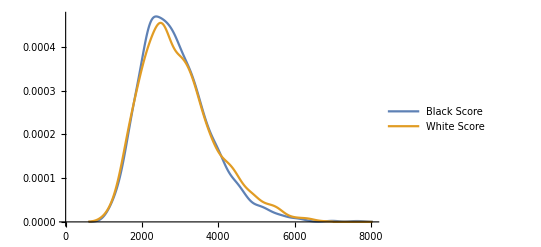

```mathematica
SmoothHistogram[{hist1[[All,2]],hist1[[All,3]]},PlotLegends->Placed[{"Black Score","White Score"},Below]]
```

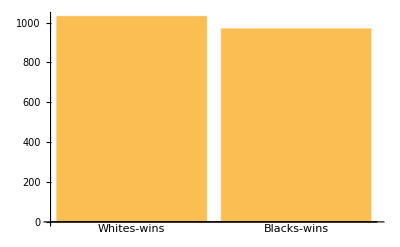

```mathematica
BarChart[Tally[hist1[[All,1]]][[All,2]],ChartLabels->Tally[hist1[[All,1]]][[All,1]]]
```

```mathematica
N[Tally[hist1[[All,1]]][[All,2]]/Total[Tally[hist1[[All,1]]][[All,2]]]]
```

{0.5155,0.4845}